```mathematica
∫(2r)/(r^2-2r+a^2)ⅆr
```

2 (ArcTan[(-1+r)/(√(-1+a^2))]/(√(-1+a^2))+1/2 Log[a^2-2 r+r^2])

```mathematica
∫a/(r^2-2r+a^2)ⅆr
```

(a ArcTan[(-1+r)/(√(-1+a^2))])/(√(-1+a^2))

```mathematica
(* i atan[ix] == atanh[-x] *)
```

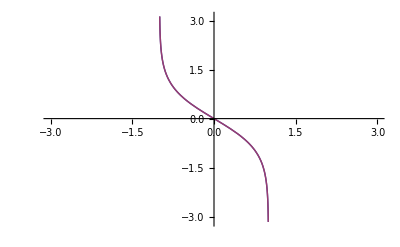

```mathematica
Plot[{I ArcTan[I x],ArcTanh[-x]},{x,-3,3}]
```

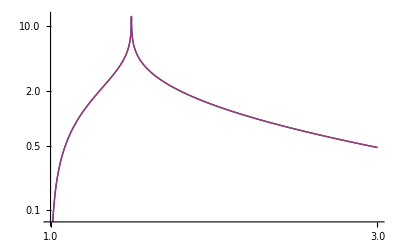

```mathematica
LogLogPlot[{Re[(-a I ArcTan[I(-1+r)/(√(+1-a^2))])/(√(1-a^2))]/.{a->.95},Re[(-a ArcTanh[-(-1+r)/(√(+1-a^2))])/(√(1-a^2))]/.{a->.95}},{r,1,3}]
```

```mathematica
(*
```